```mathematica
ClearAll[gamToString];
gamToString = {
-Ch[p_,q_]:>"("<>ToString[p]<>", "<>ToString[q]<>")[1]",
Ch[p_,q_]:>"("<>ToString[p]<>", "<>ToString[q]<>")"
};
```

```mathematica
ClearAll[GamCaption];
GamCaption[gam_,t_,psi_,m_] := Module[{s, tt,pos, dir, normal},
s = Sign[gam[[1]]];
pos[tt_]={Rays[gam/.repCh,tt,psi, m],tt};
dir = Normalize[D[pos[tt],tt]/.{tt->t}];
normal={dir[[2]],-dir[[1]]};
Text[gam/.gamToString, pos[t], -s*1.5*normal, -s*dir]
]
```

```mathematica
(* ChatGPT *)
ClearAll[QuiverDomain];
Options[QuiverDomain]={PlotStyle->LightBlue,PlotRange->{{-1.5,1.5},{0,1}},PlotPoints->100};
QuiverDomain[coll_,psi_,m_,OptionsPattern[]]:=Module[{sty=OptionValue[PlotStyle],pr=OptionValue[PlotRange],pp=OptionValue[PlotPoints],z=ZLV[#,{s,t},m]&/@coll},RegionPlot[t>0&&AllTrue[z,Re[Exp[-I psi] #]<0&],{s,pr[[1,1]],pr[[1,2]]},{t,pr[[2,1]],pr[[2,2]]},
PlotPoints->pp,
AspectRatio->1,
PlotStyle->{sty,Opacity[.5]},
BoundaryStyle->None
]];
```

## -1/3 < m < 0

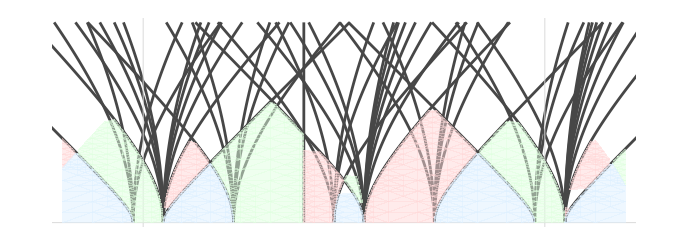

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=-1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Select[With[{L=6},Flatten[Table[{mF,mB},{mF,-L,L},{mB,-L,L}],1]], With[{z=ZLV[#,{s,t},m]&/@SpectralFlow[Coll, #]}, FullSimplify@ComplexExpand[AllTrue[z,Re[Exp[-I psi]#]<0&]&&(xmin<=s<=xmax&&0<=t<=tmax)]]=!=False&];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->20], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

## 0 < m < 1/3

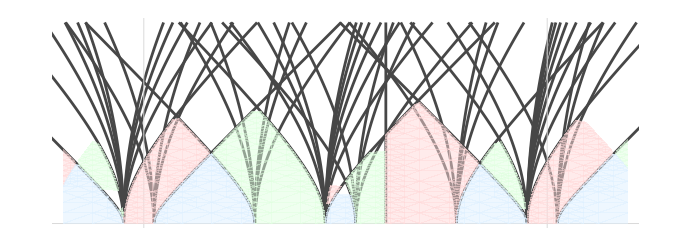

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Select[With[{L=6},Flatten[Table[{mF,mB},{mF,-L,L},{mB,-L,L}],1]], With[{z=ZLV[#,{s,t},m]&/@SpectralFlow[Coll, #]}, FullSimplify@ComplexExpand[AllTrue[z,Re[Exp[-I psi]#]<0&]&&(xmin<=s<=xmax&&0<=t<=tmax)]]=!=False&];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->20], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

## 1/3 < m < 2/3

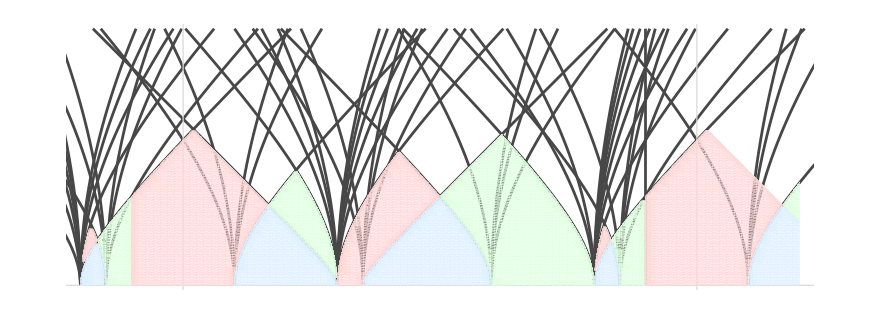

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=4/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Select[With[{L=8},Flatten[Table[{mF,mB},{mF,-L,L},{mB,-L,L}],1]], With[{z=ZLV[#,{s,t},m]&/@SpectralFlow[Coll, #]}, FullSimplify@ComplexExpand[AllTrue[z,Re[Exp[-I psi]#]<0&]&&(xmin<=s<=xmax&&0<=t<=tmax)]]=!=False&];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

```mathematica
With[{xmin=-0.2,xmax=1.2,tmax=0.5,L=8,Coll=CollArcaraII,m=4/10,psi=0},
Select[Flatten[Table[{mF,mB},{mF,-L,L},{mB,-L,L}],1], With[{z=ZLV[#,{s,t},m]&/@SpectralFlow[Coll, #]}, Echo[FullSimplify@ComplexExpand[AllTrue[z,Re[Exp[-I psi]#]<0&]&&(xmin<s<xmax&&0<t<tmax)]]]=!=False&]]
```

False

False

False

«9 more identical outputs»

441+50 t^2<5 s (31+10 s)&&121+10 s>0&&1469+200 t^2<10 s (87+20 s)&&10 s (77+20 s)<1339+200 t^2&&-0.2<s<1.2&&0<t<0.5

2369+200 t^2<10 s (57+20 s)&&131+10 s>0&&531+50 t^2<5 s (41+10 s)&&5 s (18+5 s)<243+25 t^2&&-0.2<s<1.2&&0<t<0.5

378+25 t^2<5 s (13+5 s)&&141+10 s>0&&2829+200 t^2<10 s (77+20 s)&&10 s (67+20 s)<2599+200 t^2&&-0.2<s<1.2&&0<t<0.5

3729+200 t^2<10 s (47+20 s)&&151+10 s>0&&448+25 t^2<5 s (18+5 s)&&5 s (31+10 s)<826+50 t^2&&-0.2<s<1.2&&0<t<0.5

1121+50 t^2<5 s (21+10 s)&&161+10 s>0&&4389+200 t^2<10 s (67+20 s)&&10 s (57+20 s)<4059+200 t^2&&-0.2<s<1.2&&0<t<0.5

False

False

False

«9 more identical outputs»

198+25 t^2<5 s (13+5 s)&&111+10 s>0&&1339+200 t^2<10 s (77+20 s)&&10 s (67+20 s)<1209+200 t^2&&-0.2<s<1.2&&0<t<0.5

2139+200 t^2<10 s (47+20 s)&&121+10 s>0&&243+25 t^2<5 s (18+5 s)&&5 s (31+10 s)<441+50 t^2&&-0.2<s<1.2&&0<t<0.5

686+50 t^2<5 s (21+10 s)&&131+10 s>0&&2599+200 t^2<10 s (67+20 s)&&10 s (57+20 s)<2369+200 t^2&&-0.2<s<1.2&&0<t<0.5

3399+200 t^2<10 s (37+20 s)&&141+10 s>0&&826+50 t^2<5 s (31+10 s)&&5 s (13+5 s)<378+25 t^2&&-0.2<s<1.2&&0<t<0.5

513+25 t^2<5 s (8+5 s)&&151+10 s>0&&4059+200 t^2<10 s (57+20 s)&&10 s (47+20 s)<3729+200 t^2&&-0.2<s<1.2&&0<t<0.5

False

False

False

«9 more identical outputs»

351+50 t^2<5 s (21+10 s)&&101+10 s>0&&1209+200 t^2<10 s (67+20 s)&&10 s (57+20 s)<1079+200 t^2&&-0.2<s<1.2&&0<t<0.5

1909+200 t^2<10 s (37+20 s)&&111+10 s>0&&441+50 t^2<5 s (31+10 s)&&5 s (13+5 s)<198+25 t^2&&-0.2<s<1.2&&0<t<0.5

308+25 t^2<5 s (8+5 s)&&121+10 s>0&&2369+200 t^2<10 s (57+20 s)&&10 s (47+20 s)<2139+200 t^2&&-0.2<s<1.2&&0<t<0.5

3069+200 t^2<10 s (27+20 s)&&131+10 s>0&&378+25 t^2<5 s (13+5 s)&&5 s (21+10 s)<686+50 t^2&&-0.2<s<1.2&&0<t<0.5

931+50 t^2<5 s (11+10 s)&&141+10 s>0&&3729+200 t^2<10 s (47+20 s)&&10 s (37+20 s)<3399+200 t^2&&-0.2<s<1.2&&0<t<0.5

False

False

False

«9 more identical outputs»

153+25 t^2<5 s (8+5 s)&&91+10 s>0&&1079+200 t^2<10 s (57+20 s)&&10 s (47+20 s)<949+200 t^2&&-0.2<s<1.2&&0<t<0.5

1679+200 t^2<10 s (27+20 s)&&101+10 s>0&&198+25 t^2<5 s (13+5 s)&&5 s (21+10 s)<351+50 t^2&&-0.2<s<1.2&&0<t<0.5

546+50 t^2<5 s (11+10 s)&&111+10 s>0&&2139+200 t^2<10 s (47+20 s)&&10 s (37+20 s)<1909+200 t^2&&-0.2<s<1.2&&0<t<0.5

2739+200 t^2<10 s (17+20 s)&&121+10 s>0&&686+50 t^2<5 s (21+10 s)&&5 s (8+5 s)<308+25 t^2&&-0.2<s<1.2&&0<t<0.5

418+25 t^2<5 s (3+5 s)&&131+10 s>0&&3399+200 t^2<10 s (37+20 s)&&10 s (27+20 s)<3069+200 t^2&&-0.2<s<1.2&&0<t<0.5

False

False

False

«9 more identical outputs»

261+50 t^2<5 s (11+10 s)&&81+10 s>0&&949+200 t^2<10 s (47+20 s)&&10 s (37+20 s)<819+200 t^2&&-0.2<s<1.2&&0<t<0.5

1449+200 t^2<10 s (17+20 s)&&91+10 s>0&&351+50 t^2<5 s (21+10 s)&&5 s (8+5 s)<153+25 t^2&&-0.2<s<1.2&&0<t<0.5

238+25 t^2<5 s (3+5 s)&&101+10 s>0&&1909+200 t^2<10 s (37+20 s)&&10 s (27+20 s)<1679+200 t^2&&-0.2<s<1.2&&0<t<0.5

2409+200 t^2<10 s (7+20 s)&&111+10 s>0&&308+25 t^2<5 s (8+5 s)&&5 s (11+10 s)<546+50 t^2&&-0.2<s<1.2&&0<t<0.5

5 s (1+10 s)>741+50 t^2&&-0.2<s<1.2&&10 s (27+20 s)>3069+200 t^2&&10 s (17+20 s)<2739+200 t^2&&0<t<0.5

False

False

False

«9 more identical outputs»

108+25 t^2<5 s (3+5 s)&&71+10 s>0&&819+200 t^2<10 s (37+20 s)&&10 s (27+20 s)<689+200 t^2&&-0.2<s<1.2&&0<t<0.5

1219+200 t^2<10 s (7+20 s)&&81+10 s>0&&153+25 t^2<5 s (8+5 s)&&5 s (11+10 s)<261+50 t^2&&-0.2<s<1.2&&0<t<0.5

406+50 t^2<5 s (1+10 s)&&91+10 s>0&&1679+200 t^2<10 s (27+20 s)&&10 s (17+20 s)<1449+200 t^2&&-0.2<s<1.2&&0<t<0.5

10 s (-3+20 s)>2079+200 t^2&&-0.2<s<1.2&&5 s (11+10 s)>546+50 t^2&&5 s (3+5 s)<238+25 t^2&&0<t<0.5

5 s (-2+5 s)>323+25 t^2&&-0.2<s<1.2&&10 s (17+20 s)>2739+200 t^2&&10 s (7+20 s)<2409+200 t^2&&0<t<0.5

False

False

False

«9 more identical outputs»

171+50 t^2<5 s (1+10 s)&&61+10 s>0&&689+200 t^2<10 s (27+20 s)&&10 s (17+20 s)<559+200 t^2&&-0.2<s<1.2&&0<t<0.5

989+30 s+200 t^2<200 s^2&&71+10 s>0&&261+50 t^2<5 s (11+10 s)&&5 s (3+5 s)<108+25 t^2&&-0.2<s<1.2&&0<t<0.5

5 s (-2+5 s)>168+25 t^2&&-0.2<s<1.2&&10 s (17+20 s)>1449+200 t^2&&10 s (7+20 s)<1219+200 t^2&&0<t<0.5

10 s (-13+20 s)>1749+200 t^2&&-0.2<s<1.2&&5 s (3+5 s)>238+25 t^2&&5 s (1+10 s)<406+50 t^2&&0<t<0.5

5 s (-9+10 s)>551+50 t^2&&-0.2<s<1.2&&10 s (7+20 s)>2409+200 t^2&&10 s (-3+20 s)<2079+200 t^2&&0<t<0.5

False

False

False

«9 more identical outputs»

5 s (-2+5 s)>63+25 t^2&&-0.2<s<1.2&&10 s (17+20 s)>559+200 t^2&&10 s (7+20 s)<429+200 t^2&&0<t<0.5

10 s (-13+20 s)>759+200 t^2&&-0.2<s<1.2&&5 s (3+5 s)>108+25 t^2&&5 s (1+10 s)<171+50 t^2&&0<t<0.5

5 s (-9+10 s)>266+50 t^2&&-0.2<s<1.2&&10 s (7+20 s)>1219+200 t^2&&10 s (-3+20 s)<989+200 t^2&&0<t<0.5

10 s (-23+20 s)>1419+200 t^2&&-0.2<s<1.2&&5 s (1+10 s)>406+50 t^2&&5 s (-2+5 s)<168+25 t^2&&0<t<0.5

5 s (-7+5 s)>228+25 t^2&&-0.2<s<1.2&&10 s (-3+20 s)>2079+200 t^2&&10 s (-13+20 s)<1749+200 t^2&&0<t<0.5

False

False

False

«6 more identical outputs»

10 s (-3+20 s)>9+200 t^2&&9+55 s+50 s^2>50 t^2&&2+5 s (3+5 s)<25 t^2&&t>0

False

False

5 s (-9+10 s)>81+50 t^2&&-0.2<s<1.2&&10 s (7+20 s)>429+200 t^2&&10 s (-3+20 s)<299+200 t^2&&0<t<0.5

10 s (-23+20 s)>529+200 t^2&&-0.2<s<1.2&&5 s (1+10 s)>171+50 t^2&&5 s (-2+5 s)<63+25 t^2&&0<t<0.5

5 s (-7+5 s)>98+25 t^2&&-0.2<s<1.2&&10 s (-3+20 s)>989+200 t^2&&10 s (-13+20 s)<759+200 t^2&&0<t<0.5

10 s (-33+20 s)>1089+200 t^2&&-0.2<s<1.2&&5 s (-2+5 s)>168+25 t^2&&5 s (-9+10 s)<266+50 t^2&&0<t<0.5

50 s^2>361+95 s+50 t^2&&-0.2<s<1.2&&10 s (-13+20 s)>1749+200 t^2&&10 s (-23+20 s)<1419+200 t^2&&0<t<0.5

False

False

False

«6 more identical outputs»

21+10 s (-13+20 s)>200 t^2&&s>-0.1&&2+5 s (3+5 s)>25 t^2&&5 s (1+10 s)<1+50 t^2&&t>0

False

False

5 s (-7+5 s)>18+25 t^2&&-0.2<s<1.2&&10 s (-3+20 s)>299+200 t^2&&10 s (-13+20 s)<169+200 t^2&&0<t<0.5

10 s (-33+20 s)>299+200 t^2&&-0.2<s<1.2&&5 s (-2+5 s)>63+25 t^2&&5 s (-9+10 s)<81+50 t^2&&0<t<0.5

50 s^2>126+95 s+50 t^2&&-0.2<s<1.2&&10 s (-13+20 s)>759+200 t^2&&10 s (-23+20 s)<529+200 t^2&&0<t<0.5

10 s (-43+20 s)>759+200 t^2&&-0.2<s<1.2&&5 s (-9+10 s)>266+50 t^2&&5 s (-7+5 s)<98+25 t^2&&0<t<0.5

5 s (-12+5 s)>133+25 t^2&&-0.2<s<1.2&&10 s (-23+20 s)>1419+200 t^2&&10 s (-33+20 s)<1089+200 t^2&&0<t<0.5

False

False

False

«7 more identical outputs»

12+5 s (-7+5 s)>25 t^2&&10 s (-3+20 s)>9+200 t^2&&21+10 s (-13+20 s)<200 t^2&&t>0

False

False

False

5 s (-12+5 s)>28+25 t^2&&-0.2<s<1.2&&10 s (-23+20 s)>529+200 t^2&&10 s (-33+20 s)<299+200 t^2&&0<t<0.5

10 s (-53+20 s)>429+200 t^2&&-0.2<s<1.2&&5 s (-7+5 s)>98+25 t^2&&50 s^2<126+95 s+50 t^2&&0<t<0.5

5 s (-29+10 s)>171+50 t^2&&-0.2<s<1.2&&10 s (-33+20 s)>1089+200 t^2&&10 s (-43+20 s)<759+200 t^2&&0<t<0.5

False

False

False

«8 more identical outputs»

221+10 s (-43+20 s)>200 t^2&&4+5 s (-9+10 s)>50 t^2&&12+5 s (-7+5 s)<25 t^2&&t>0

False

False

False

«1 more identical outputs»

5 s (-17+5 s)>38+25 t^2&&-0.2<s<1.2&&10 s (-43+20 s)>759+200 t^2&&10 s (-53+20 s)<429+200 t^2&&0<t<0.5

False

False

False

«8 more identical outputs»

10 (53-20 s) s+200 t^2<351&&10 s>9&&5 (7-5 s) s+25 t^2<12&&44+50 s^2<95 s+50 t^2&&t>0

False

False

False

«70 more identical outputs»

{{-8,4},{-8,5},{-8,6},{-8,7},{-8,8},{-7,4},{-7,5},{-7,6},{-7,7},{-7,8},{-6,4},{-6,5},{-6,6},{-6,7},{-6,8},{-5,4},{-5,5},{-5,6},{-5,7},{-5,8},{-4,4},{-4,5},{-4,6},{-4,7},{-4,8},{-3,4},{-3,5},{-3,6},{-3,7},{-3,8},{-2,4},{-2,5},{-2,6},{-2,7},{-2,8},{-1,4},{-1,5},{-1,6},{-1,7},{-1,8},{0,1},{0,4},{0,5},{0,6},{0,7},{0,8},{1,1},{1,4},{1,5},{1,6},{1,7},{1,8},{2,2},{2,6},{2,7},{2,8},{3,3},{3,8},{4,3}}

```mathematica
temp = With[{xmin=-0.2,xmax=1.2,tmax=0.5,L=6,Coll=CollArcaraII,m=4/10,psi=0, possibleSpecParams=%,Color=LightRed},
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->30], {spec,possibleSpecParams}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

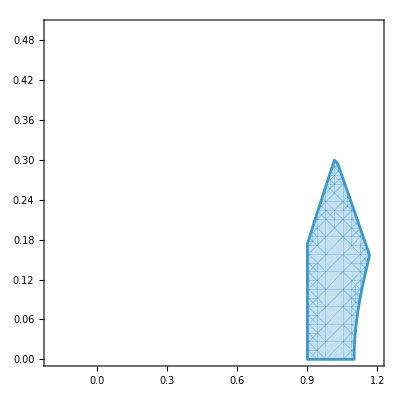

```mathematica
RegionPlot[10 (53-20 s) s+200 t^2<351&&10 s>9&&5 (7-5 s) s+25 t^2<12&&44+50 s^2<95 s+50 t^2&&t>0, {s,-0.2,1.2},{t,0,0.5}]
```